### DSC 101: Mon 4 Nov

#### Commands covered

Stan Wagon, Mathematica in Action, chapter 7.

There are no new “important” commands. The text uses several old and a few new functions and options, which you can look up as needed. One important use, which we have seen but not emphasized, is to use the two-argument N[] to achieve an accurate result. Perhaps the most interesting new function is RSolve[], which tries to find a formula for “recurrences.” The equation for an iteration, x_(n+1)=f(x_n), is a type of recurrence. The kind of formula RSolve[] tries to find is one in terms of the index variable n only, that is, a formula of the form x_n=g(n). It cannot always be done. However, when it succeeds, we call the formula g(n) a “closed-form solution” of the recurrence.

##### Important:

```mathematica
N[exact,70] (* the concept of adaptive precision *)
```

##### Secondary:

```mathematica
RSolve
WorkingPrecision
Plot3D
```

##### Unimportant

Any others.

A few of them might be of interest to someone wanting to explore Mathematica on their own:

```mathematica
Evaluate
Compile
Riffle
Partition
Transpose
Union
Thickness,PointSize
GraphicsRow,GraphicsColumn,GraphicsGrid
```

### Brief notes on definitions and concepts of convergence

x_(n+1)=f(x_n): iteration of f, sequence of iterates x_n. The initial value x_0 may be specified or freely chosen, depending on the problem.

x_*=f(x_*): a fixed point x_* is a solution of this equation.

E_n=x_n-x_*: the error at step n, which is the difference between an iterate and a fixed point; the iterates x_n are said to converge to a fixed point x_* if the error becomes as small as we please for n large enough. If there are multiple fixed points, one can remove the ambiguity by specifying exactly which fixed point is being discussed.

R_n=(f(x_n)-f(x_*))/(x_n-x_*): the convergence rate at step n (or sometimes divergence rate if R_n>1). Since f(x_n)-f(x_*)=x_(n+1)-x_*=E_(n+1), we have the relation E_(n+1)=R_n E_n. First convergence criterion: As was shown in class, if |R_n|<=r<1, then |E_n|<=r^n E_0, and x_n will converge to the fixed point x_*.

Second convergence criterion: If the derivative f'(x) is continuous at a fixed point x_* and |f'(x_*)|<1, then in some open interval extending an equal distance on either side of x_*, the rate formula will satisfy |(f(x)-f(x_*))/(x-x_*)|<=r<1 for some value of r and all x in the interval. In that case, once an iterate falls inside the open interval, all subsequent iterates will stay in the interval, the error will decrease, and x_n will converge to the fixed point x_*.

Nesting functions: Sometimes one writes f^k for the k-fold composition; that is, f^3(x)=f(f(f(x))) for n=3, say. For the logistic (quadratic) map, this would be f_r^k(x_0), which is bit complicated and Wagon avoids in Mathematica in Action. On the other hand, it saves writing lots of fs and parentheses.

Orbits: The orbit of a point x_0 is the set of values {x_0,x_1,x_2,x_3,...} that come from iterating f. Recall that by definition, a set contains an element only once. So the set {1,2,1,4,1,3,2,5} is the same as the set {1,2,3,4,5}. While the number of iterates x_n is infinite, it is possible that the set of values is finite if values are repeated. Of particular interest are the periodic orbits: These are finite orbits that arise when we happen to get x_0 back again: x_0=f(x_(k-1)) for some integer k. Equivalently, we could write this condition in terms of the k-fold composition of f as x_0=f^k(x_0), for some integer k. A fixed point has a periodic orbit of length 1: If x_0=x_*, then f(x_0)=f(x_*)=x_*=x_0, and the orbit is the set {x_0}. A periodic orbit {x_0,x_1} of length 2 satisfies the equation x_0=f(x_1), where by definition x_1=f(x_0). A periodic orbit has length k if k is the smallest positive integer such that x_0=f(x_(k-1)). Stan Wagon calls such orbits cycles.

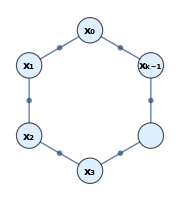

```mathematica
Graph[RotateLeft@{
Subscript[x,0]->Subscript[x,1],
Subscript[x,1]->Subscript[x,2],
Subscript[x,2]->Subscript[x,3],
Subscript[x,3]->SpanFromLeft,
SpanFromLeft->Subscript[x,k-1],
Subscript[x,k-1]->Subscript[x,0]},
VertexShapeFunction->Function[{c,n,s},{LightBlue,Disk[c,8s],Text[Style[n,Bold,Black],c]}],
EdgeLabels->Graphics[{{ColorData[97][1],Opacity[0.8],Disk[{0,0}]},White,Text[Style[f,16]]},ImageSize->20],
EdgeShapeFunction->{{"FilledArrow","ArrowSize"->.1}},
ImageSize->Small]
```

Attracting and repelling periodic orbits (or cycles): Suppose the orbit of x_0 is periodic of period k, so that x_0=f^k(x_0). Then the orbit is attracting if for any x that is sufficiently close to x_0, every kth iterate of x converges to x_0. Or in terms of the convergence criteria,
	(1)|(f^k(x)-f^k(x_0))/(x-x_0)|<=r<1   or   (2) |d/dx f^k(x)|<1 at x=x_0.
If the rate (1) or derivative (2) is greater than 1 in magnitude, the orbit is repelling.

Choatic: See p. 196.

The Lyapunov exponent λ components:
	δ = a small distance. Technically, the definition is in terms of the limit as δ approaches zero, but computationally, we will choose a small positive number for δ. The name for δ is (small or lower-case) delta.
	n= the number of times that the function f is iterated. The variable n is often thought of as the number of time periods, such as days or years, that have elapsed, and f represents a process that affects a quantity x, such as a population, every day or every year etc. The Lyapunov exponent measures the long-term behavior. This means n should be large. Technically the definition is in terms of the limit as n approaches infinity. 
	Δ=|f^n(x_0+1/2 δ)-f^n(x_0-1/2 δ)|=|f(f(f(⋯f(x_0+1/2 δ)⋯)))-f(f(f(⋯f(x_0-1/2 δ)⋯)))|, the (symmetric) difference in values if the n-fold composition of f near some point x_0 in the domain.

The formula:
	λ≈1/n log Δ/δ=1/n log((|f^n(x_0+1/2 δ)-f^n(x_0-1/2 δ)|)/δ) for n large and δ small and positive.
Code for the formula for the logistic function f_r is provided in the 07_CODE.nb notebook on Canvas. In practice, for the logistic function, n=100 seems large enough and δ=1/10 seems small enough. The name for λ is (small or lower-case) lambda.
	λ= exponential rate of separation (or spread). If the Lyapunov exponent is positive, then function values separate as n increases, and roundoff error builds up exponentially when using approximate reals. If the Lyapunov exponent is negative, then the iteration is stable.

Dividing by log 10 (p. 199): Recall that in Mathematica log x is the same as the natural logarithm ln x. Dividing by log(10) converts the natural logarithm to the base-10 logarithm:
	log_10 x=(log x)/(log 10)
The value of log_10 x is roughly equal to the number of digits from the decimal point at which the leading decimal of x is located. It’s to the left of the decimal if the logarithm is positive and to the right if it is negative.

Bifurcation: There does not seem to be a definition in Mathematica in Action, at least not in chapter 7. For the logistic map f_r, a value r=r_b is a bifurcation point if the attracting cycles for r<r_b are different than the attracting cycles for r>r_b, for all r sufficiently close to r_b.

### Sqrt map

#### Basic definitions and review

Recall from last class, the sequence of iterates is given by
	x_(n+1)=1/2(x_n+r/x_n)
where r is a positive number and the initial value x_0 is positive and either given or chosen at random.

One can show that the fixed point of iterating babylonian[r] is Sqrt[r].

```mathematica
ClearAll[babylonian];
babylonian[r_][x_]:=1/2(x+r/x);
babylonian[r][x]
```

1/2 (r/x+x)

E_(n+1)

```mathematica
babylonian[r][Subscript[x, n]]-Sqrt[r]//Simplify
```

(√r-x_n)^2/(2 x_n)

R_(n+1)

```mathematica
(babylonian[r][Subscript[x, n]]-Sqrt[r])/(Subscript[x, n]-Sqrt[r])//Simplify//Together
```

(-√r+x_n)/(2 x_n)

New: Plot3D for visualizing R_n as a function of x=x_n for different values of r:

```mathematica
Plot3D[Abs[(babylonian[r][x]-Sqrt[r])/(x-Sqrt[r])],
{r,0.1,10},{x,Sqrt[r]/2,10},
PlotStyle->Opacity[0.5],MeshFunctions->{#1&},Mesh->{Exp@Subdivide[Log[0.1],Log[10],9]},
MeshStyle->Directive[ColorData[97][1],Thick],ScalingFunctions->{"Log",Automatic}]
```

-Graphics3D-

#### √256789

##### Machine precision (“hardware reals”)

```mathematica
seq=NestList[babylonian[256789],500.,5];
err=%-Sqrt[256789];
```

```mathematica
seq//Column
err//Column
```

500.
506.789
506.744
506.744
506.744
506.744

-6.74352
0.0454751
2.04028×10^-6
5.68434×10^-14
5.68434×10^-14
5.68434×10^-14

##### Precision 40 (“software reals”)

```mathematica
seq=NestList[babylonian[256789],500.`40,5];
err=%-Sqrt[256789];
```

```mathematica
seq//Column
err//Column
```

500.
506.789
506.7435269125809755144645996657386012719
506.7435248722967196733808456919364008715
506.7435248722967155660172186164325512771
506.7435248722967155660172186164325346312

-6.7435248722967155660172186164325346312
0.045475127703284433982781383567465369
2.040284259948447381049306066641×10^-6
4.10736362707550386624×10^-15
1.6646×10^-32
0.

E_n:

```mathematica
err^2/(2seq)//Column
```

0.04547512770328443398278138356746536881
2.0402842599484473810493060666407396×10^-6
4.107363627075503866240330393476×10^-15
1.664593145938502016351×10^-32
2.734×10^-67
0.

##### Adaptive precision

We must start with exact numbers.

```mathematica
seq=NestList[babylonian[2],500,5];
err=%-Sqrt[2];
```

Inspect initial values:

```mathematica
seq//Column
err//Column
```

Ask for 40 digits. As happens in Mathematica in Action, some calculations run into an internal precision that we need to increase.

```mathematica
N[seq,40]//Column
N[err,40]//Column
```

Try again after raising the limit:

```mathematica
$MaxExtraPrecision=100;
N[seq,40]//Column
N[err,40]//Column
$MaxExtraPrecision=50;
```

```mathematica
N[err^2/(2seq),40]//Column
```

```mathematica
{{0.0454751277032844339827813835674653688099048366961411392741`37.8259681186489}, {2.0402842599484473810493060666407396428538985666062827`35.651897267239185*^-6}, {4.1073636270755038662403303934761357792518001`31.303872472847015*^-15}, {1.664593145938502016350734946088447420550325074`22.60774494919121*^-32}, {2.73399679078654217780709207954`5.21548989838242*^-67}, {0``77.5962417876432}}
```

0.04547512770328443398278138356746536881
2.0402842599484473810493060666407396×10^-6
4.107363627075503866240330393476×10^-15
1.664593145938502016351×10^-32
2.734×10^-67
0.

#### Class activity

Determine simple formulas for E_(n+1) and R_n in terms of x, r, and E_n.

Questions for inquiry:

When is the error E_(n+1) smaller than E_n?

Are the conditions for E_(n+1) to be smaller than E_n always achieved?

Given r, for which initial values of x_0 does the sequence of iterates converge to √r?

What does the (simplified) formula for E_(n+1) imply about the rate of convergence of the iterates?

For a given r, are there initial values for which the convergence is slow?

#### Mini-project 4

In a well-written, well-edited notebook, report on the inquiry in the class activity. The goal is to convey a complete understanding of the convergence of the sequence to √r. Support sentences with code that calculates what is being claimed.